```mathematica
<<MaTeX`
SetOptions[MaTeX,"Preamble"->{"\\usepackage{amsmath,amssymb,amsfonts}","\\usepackage{lmodern}"}];
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/dadhikar/Library/CloudStorage/OneDrive-KennesawStateUniversity(2)/MyBooks/A_ODE_Project/chap07/Mathematica

{{x1[t]→1/5 (Sin[t]-√6 Sin[√6 t]),x2[t]→1/10 (4 Sin[t]+√6 Sin[√6 t])}}

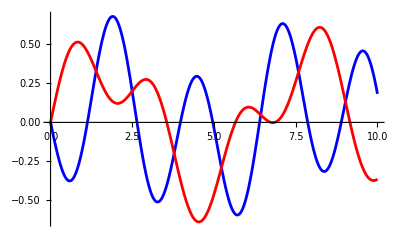

7-6-1.pdf

\left\{\frac{1}{5} \left(\sin (t)-\sqrt{6} \sin \left(\sqrt{6} t\right)\right),\frac{1}{10} \left(4 \sin (t)+\sqrt{6} \sin \left(\sqrt{6} t\right)\right)\right\}

```mathematica
(*Define the system*)
textStyle={FontFamily->"LM Roman 12",FontSize->30};sol=DSolve[{x1''[t]==-5x1[t]+2x2[t],x2''[t]==2x1[t]-2x2[t],x1[0]==0,x1'[0]==-1,x2[0]==0,x2'[0]==1},{x1[t],x2[t]},t]

(*To extract and display the solutions*)
x1sol=x1[t]/. sol[[1]];
x2sol=x2[t]/. sol[[1]];
TeXForm[{x1sol,x2sol}]

(*Optional:Plot the solutions*)
plot1:=Plot[{x1sol,x2sol},{t,0,10},PlotLegends->SwatchLegend[MaTeX[{"x_1(t)", "x_2(t)"},Magnification->1.8]],PlotStyle->{Blue,Red},
AxesLabel->{MaTeX["t",Magnification->2],MaTeX["",Magnification->2]}, AxesStyle->Directive[FontSize->20,FontFamily->"LM Roman 12"], 
(*Epilog->{Inset[MaTeX["Solutions",Magnification->2],{4,.6},Scaled[{.1,.5}]]},*)
LabelStyle->Directive[FontSize->12,FontFamily->"LM Roman 12"]]
plot1
Export["7-6-1.pdf",plot1]
```